# Plotting the results of the Julia code for REPINs and RAYTs

## With benefit

With the chosen parameters in the Julia code the expected average REPINS is given by 1/(1-0.985)Log[10^-2/(10^-3(2 0.95-1))] = 160.53

### Starting with an initial condition close to full REPINS

```mathematica
rawdata02=Import[NotebookDirectory[]<>"Raytssol2_withbenefits.csv","CSV"];
topl02=Table[rawdata02⟦2;;,{1,i}⟧,{i,2,Length[rawdata02⟦1⟧],1}];
```

```mathematica
kmax=(Length[rawdata02⟦1⟧]-1)/3
```

1053

```mathematica
rawdata02//Dimensions
```

{102,3160}

```mathematica
Manipulate[ListPlot[rawdata02⟦i,kmax+1;;2 kmax⟧,Joined->True,PlotRange->{Automatic,{-0.01,0.2}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis],{i,2,rawdata02//Length,1}]
```

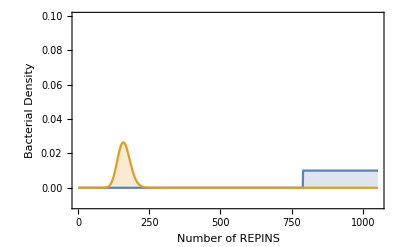

```mathematica
ListPlot[{rawdata02⟦2,kmax+1;;2 kmax⟧,rawdata02⟦rawdata02//Length,kmax+1;;2 kmax⟧},Joined->True,PlotRange->{Automatic,{-0.01,0.1}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis]
```

```mathematica
topllist02=Table[rawdata02⟦i,kmax+1;;2 kmax⟧,{i,2,rawdata02//Length,10}];
```

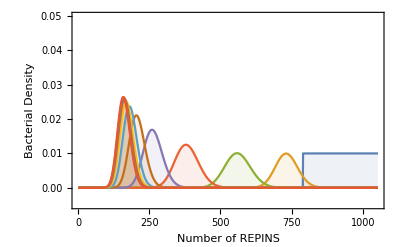

```mathematica
ListPlot[topllist02,Joined->True,PlotRange->{Automatic,{-0.005,0.05}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis,FillingStyle->Opacity[0.1]]
```

```mathematica
variablestoplot02=Range[kmax+1,2 kmax,1];
```

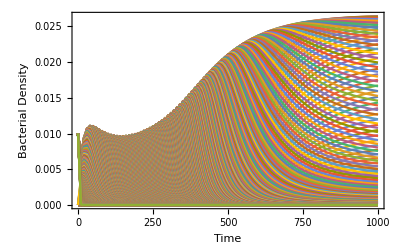

```mathematica
ListPlot[topl02⟦kmax+1;;2 kmax⟧,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Time","Bacterial Density"}]
```

The REPINS take over the bacterial genome eventually driving the extinction of the whole bacterial population irrespective of the RAYTs

### Starting with an initial condition close to no REPINS

```mathematica
rawdata03=Import[NotebookDirectory[]<>"Raytssol3_withbenefits.csv","CSV"];
topl03=Table[rawdata03⟦2;;,{1,i}⟧,{i,2,Length[rawdata03⟦1⟧],1}];
```

```mathematica
rawdata03//Length
```

102

```mathematica
Manipulate[ListPlot[rawdata03⟦i,(kmax+2);;(2 kmax)⟧,Joined->True,PlotRange->{Automatic,{-0.01,0.2}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]}],{i,2,rawdata03//Length,1}]
```

```mathematica
topllist=Table[rawdata03⟦i,(kmax+2);;(2 kmax)⟧,{i,2,rawdata03//Length,2}];
```

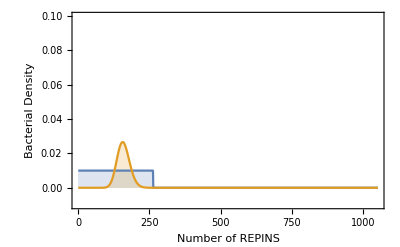

```mathematica
ListPlot[{rawdata03⟦2,(kmax+2);;(2 kmax)⟧,rawdata03⟦rawdata03//Length,(kmax+2);;(2 kmax)⟧},Joined->True,PlotRange->{Automatic,{-0.01,0.1}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis]
```

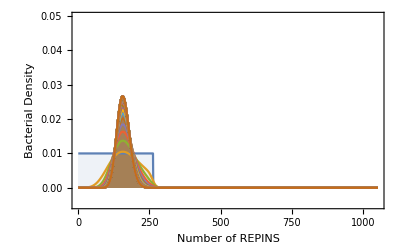

```mathematica
ListPlot[topllist,Joined->True,PlotRange->{Automatic,{-0.005,0.05}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis,FillingStyle->Opacity[0.1]]
```

```mathematica
variablestoplot03=Range[(kmax+1),(2 kmax),1];
```

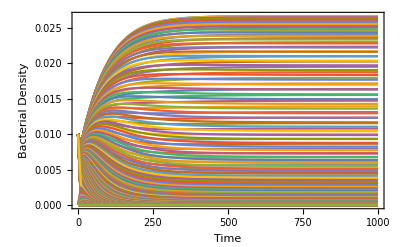

```mathematica
ListPlot[topl03⟦variablestoplot03⟧,Joined->True,PlotRange->All,Frame->True,FrameLabel->{Style["Time",16],Style["Bacterial Density",16]}]
```

The REPINS take over the bacterial genome eventually driving the extinction of the whole bacterial population irrespective of the RAYTs

## With no benefit

### Starting with an initial condition close to full REPINS

```mathematica
rawdata02withoutbenefits=Import[NotebookDirectory[]<>"Raytssol2_withoutbenefits.csv","CSV"];
lengthofrawdata02withoutbenefits=Length[rawdata02withoutbenefits];
topl02benefits=Table[rawdata02withoutbenefits⟦2;;,{1,i}⟧,{i,2,Length[rawdata02withoutbenefits⟦1⟧],1}];
```

```mathematica
kmax=(Length[rawdata02withoutbenefits⟦1⟧]-1)/3
```

500

```mathematica
Manipulate[ListPlot[rawdata02withoutbenefits⟦i,kmax+2;;2 kmax⟧,Joined->True,PlotRange->{Automatic,{-0.01,0.2}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis],{i,2,lengthofrawdata02withoutbenefits,1}]
```

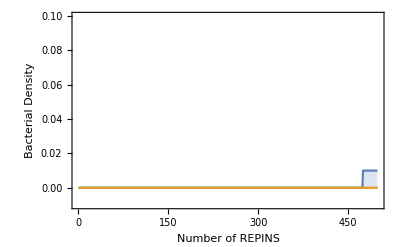

```mathematica
ListPlot[{rawdata02withoutbenefits⟦2,kmax+2;;2 kmax⟧,rawdata02withoutbenefits⟦lengthofrawdata02withoutbenefits,kmax+1;;2 kmax⟧},Joined->True,PlotRange->{Automatic,{-0.01,0.1}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis]
```

```mathematica
topllist02withoutbenefits=Table[rawdata02withoutbenefits⟦i,kmax+1;;2 kmax⟧,{i,2,lengthofrawdata02withoutbenefits,2}];
```

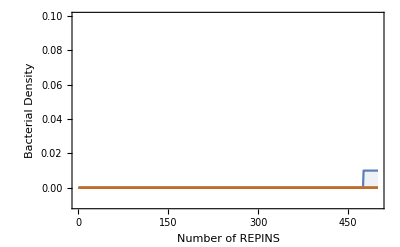

```mathematica
ListPlot[topllist02withoutbenefits,Joined->True,PlotRange->{Automatic,{-0.01,0.1}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis,FillingStyle->Opacity[0.1]]
```

```mathematica
variablestoplot02=Range[1054,2106,1];
```

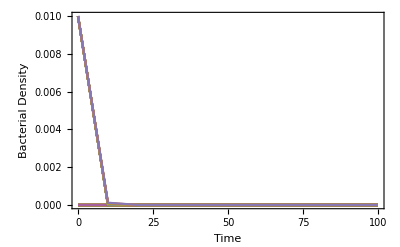

```mathematica
ListPlot[topl02benefits⟦kmax+1;;2 kmax⟧,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Time","Bacterial Density"}]
```

The REPINS take over the bacterial genome eventually driving the extinction of the whole bacterial population irrespective of the RAYTs

### Starting with an initial condition close to no REPINS

```mathematica
rawdata03nobenefits=Import[NotebookDirectory[]<>"Raytssol3_withoutbenefits.csv","CSV"];
lengthofrawdata03nobenefits=rawdata03nobenefits//Length;
topl03nobenefits=Table[rawdata03nobenefits⟦2;;,{1,i}⟧,{i,2,Length[rawdata03nobenefits⟦1⟧],1}];
```

```mathematica
rawdata03nobenefits//Dimensions
```

{12,1501}

```mathematica
lengthofrawdata03nobenefits
```

12

```mathematica
Manipulate[ListPlot[rawdata03nobenefits⟦i,(kmax+2);;(2 kmax)⟧,Joined->True,PlotRange->{Automatic,{-0.01,0.2}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]}],{i,2,lengthofrawdata03nobenefits,1}]
```

```mathematica
topllistnobenefits=Table[rawdata03nobenefits⟦i,(kmax+1);;(2 kmax)⟧,{i,2,lengthofrawdata03nobenefits,2}];
```

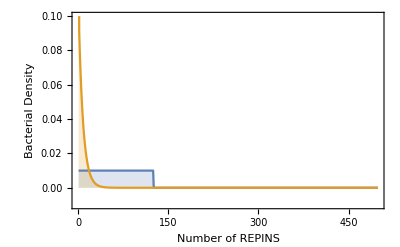

```mathematica
ListPlot[{rawdata03nobenefits⟦2,(kmax+2);;(2 kmax)⟧,rawdata03nobenefits⟦lengthofrawdata03nobenefits,(kmax+2);;(2 kmax)⟧},Joined->True,PlotRange->{Automatic,{-0.01,0.1}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis]
```

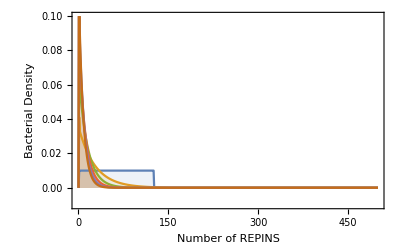

```mathematica
ListPlot[topllistnobenefits,Joined->True,PlotRange->{Automatic,{-0.01,0.1}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis,FillingStyle->Opacity[0.1]]
```

```mathematica
variablestoplot03=Range[(kmax+1),(2 kmax),1];
```

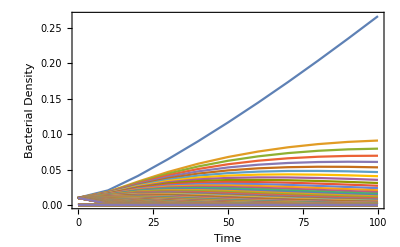

```mathematica
ListPlot[topl03nobenefits⟦variablestoplot03⟧,Joined->True,PlotRange->All,Frame->True,FrameLabel->{Style["Time",16],Style["Bacterial Density",16]}]
```

The REPINS take over the bacterial genome eventually driving the extinction of the whole bacterial population irrespective of the RAYTs

## With RAYTS

## With benefits

### Initial condition1

```mathematica
rawrayts01=Import[NotebookDirectory[]<>"Raytssol2_withRAYTS.csv","CSV"];
toplrawrayts=Table[rawrayts01⟦2;;,{1,i}⟧,{i,2,Length[rawrayts01⟦1⟧],1}];
```

```mathematica
kmax=(Length[rawrayts01⟦1⟧]-1)/3
```

1053

```mathematica
plotdetails={PlotRange->{Automatic,{-0.01,0.1}},Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis,FillingStyle->Opacity[0.1],GridLines->{None,{0.03}},GridLinesStyle->Directive[Black,Thickness[0.002]]};Manipulate[GraphicsRow[{ListPlot[rawrayts01⟦i,2;;kmax+1⟧,plotdetails],
ListPlot[rawrayts01⟦i,kmax+2;;2kmax+1⟧,plotdetails],
ListPlot[rawrayts01⟦i,2kmax+2;;3 kmax+1⟧,plotdetails]},ImageSize->1000],{i,2,rawrayts01//Length,1}]
```

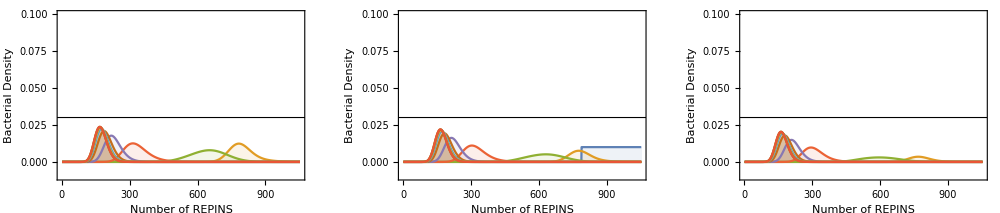

```mathematica
GraphicsRow[{ListPlot[Table[rawrayts01⟦i,2;;kmax+1⟧,{i,2,rawrayts01//Length,10}],plotdetails],
ListPlot[Table[rawrayts01⟦i,kmax+2;;2kmax+1⟧,{i,2,rawrayts01//Length,10}],plotdetails],
ListPlot[Table[rawrayts01⟦i,2kmax+2;;3 kmax+1⟧,{i,2,rawrayts01//Length,10}],plotdetails]},ImageSize->1000]
```

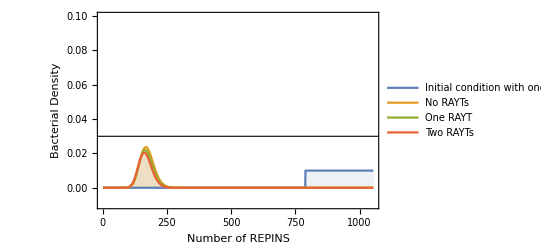

```mathematica
ListPlot[{rawrayts01⟦2,kmax+2;;2kmax+1⟧,rawrayts01⟦rawrayts01//Length,2;;kmax+1⟧,rawrayts01⟦rawrayts01//Length,kmax+2;;2kmax+1⟧,rawrayts01⟦rawrayts01//Length,2kmax+2;;3 kmax+1⟧},plotdetails,PlotLegends->{"Initial condition with one RAYT","No RAYTs","One RAYT","Two RAYTs"}]
```

```mathematica
ListPlot[{
Callout[rawrayts01⟦2,kmax+2;;2kmax+1⟧,Style["Initial\n distribution",12],{800,0.012},{800,0.01}],Callout[rawrayts01⟦rawrayts01//Length,2;;kmax+1⟧,Style["No RAYTs",12],{220,0.035},190],
Callout[rawrayts01⟦rawrayts01//Length,kmax+2;;2kmax+1⟧,Style["One RAYT",12],{250,0.015},200],
Callout[rawrayts01⟦rawrayts01//Length,2kmax+2;;3 kmax+1⟧,Style["Two RAYTs",12],{250,0.01},210]},PlotRange->{Automatic,{-0.005,0.05}},Joined->True,Frame->True,PlotStyle->{Directive[Automatic,Opacity[0.3]],Directive[ColorData[97,"ColorList"]⟦4⟧,Opacity[0.5]],Directive[ColorData[97,"ColorList"]⟦4⟧,Opacity[0.5]],Directive[ColorData[97,"ColorList"]⟦4⟧,Opacity[0.5]]},FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis,GridLines->{None,{0.022}},GridLinesStyle->Directive[Black,Thickness[0.002]],PlotLegends->{"Initial condition with one RAYT","No RAYTs","One RAYT","Two RAYTs"}]
```

-Graphics-

```mathematica
toplrawrayts//Dimensions
```

{3159,101,2}

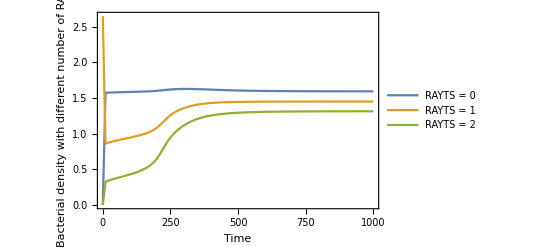

```mathematica
ListPlot[{Table[toplrawrayts⟦i⟧⟦All,2⟧,{i,1,kmax,1}]//Total,Table[toplrawrayts⟦i⟧⟦All,2⟧,{i,kmax+1,2 kmax,1}]//Total,Table[toplrawrayts⟦i⟧⟦All,2⟧,{i,2 kmax+1,3 kmax,1}]//Total},Joined->True,DataRange->{0,1000},Frame->True,FrameLabel->{"Time","Bacterial density with different number of RAYTS"},PlotLegends->{"RAYTS = 0","RAYTS = 1","RAYTS = 2"}]
```

### Initialcondition 2

```mathematica
rawrayts02=Import[NotebookDirectory[]<>"Raytssol3_withRAYTS.csv","CSV"];
toplrawrayts02=Table[rawrayts02⟦2;;,{1,i}⟧,{i,2,Length[rawrayts02⟦1⟧],1}];
```

```mathematica
kmax=(Length[rawrayts02⟦1⟧]-1)/3
```

1053

```mathematica
plotdetails={PlotRange->{Automatic,{-0.01,0.1}},Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis,FillingStyle->Opacity[0.1],GridLines->{None,{0.03}},GridLinesStyle->Directive[Black,Thickness[0.002]]};
```

```mathematica
Manipulate[GraphicsRow[{ListPlot[rawrayts02⟦i,2;;kmax+1⟧,plotdetails],
ListPlot[rawrayts02⟦i,kmax+2;;2kmax+1⟧,plotdetails],
ListPlot[rawrayts02⟦i,2kmax+2;;3 kmax+1⟧,plotdetails]},ImageSize->1000],{i,2,rawrayts02//Length,1}]
```

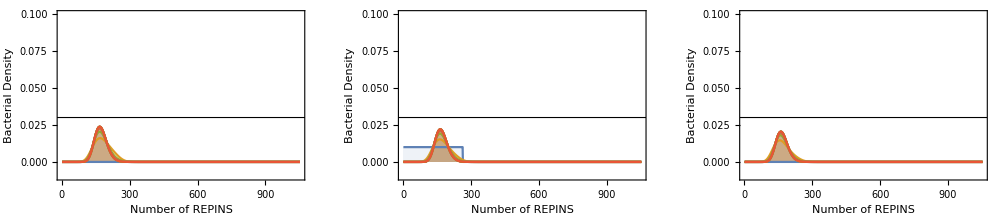

```mathematica
GraphicsRow[{ListPlot[Table[rawrayts02⟦i,2;;kmax+1⟧,{i,2,rawrayts02//Length,10}],plotdetails],
ListPlot[Table[rawrayts02⟦i,kmax+2;;2kmax+1⟧,{i,2,rawrayts02//Length,10}],plotdetails],
ListPlot[Table[rawrayts02⟦i,2kmax+2;;3 kmax+1⟧,{i,2,rawrayts02//Length,10}],plotdetails]},ImageSize->1000]
```

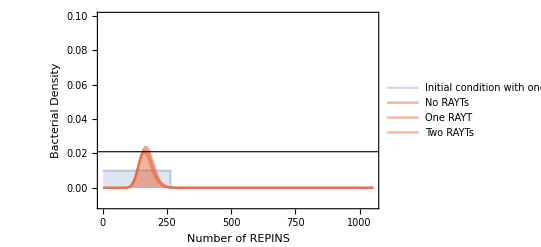

```mathematica
ListPlot[{rawrayts02⟦2,kmax+2;;2kmax+1⟧,rawrayts02⟦rawrayts02//Length,2;;kmax+1⟧,rawrayts02⟦rawrayts02//Length,kmax+2;;2kmax+1⟧,rawrayts02⟦rawrayts02//Length,2kmax+2;;3 kmax+1⟧},PlotRange->{Automatic,{-0.01,0.1}},Joined->True,Frame->True,PlotStyle->{Directive[Automatic,Opacity[0.3]],Directive[ColorData[97,"ColorList"]⟦4⟧,Opacity[0.5]],Directive[ColorData[97,"ColorList"]⟦4⟧,Opacity[0.5]],Directive[ColorData[97,"ColorList"]⟦4⟧,Opacity[0.5]]},FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis,GridLines->{None,{0.021}},GridLinesStyle->Directive[Black,Thickness[0.002]],PlotLegends->{"Initial condition with one RAYT","No RAYTs","One RAYT","Two RAYTs"}]
```

```mathematica
ListPlot[{
Callout[rawrayts02⟦2,kmax+2;;2kmax+1⟧,Style["Initial\n distribution",12],{110,0.035},110],Callout[rawrayts02⟦rawrayts02//Length,2;;kmax+1⟧,Style["No RAYTs",12],{220,0.035},190],
Callout[rawrayts02⟦rawrayts02//Length,kmax+2;;2kmax+1⟧,Style["One RAYT",12],{250,0.015},200],
Callout[rawrayts02⟦rawrayts02//Length,2kmax+2;;3 kmax+1⟧,Style["Two RAYTs",12],{250,0.01},210]},PlotRange->{Automatic,{-0.005,0.05}},Joined->True,Frame->True,PlotStyle->{Directive[Automatic,Opacity[0.3]],Directive[ColorData[97,"ColorList"]⟦4⟧,Opacity[0.5]],Directive[ColorData[97,"ColorList"]⟦4⟧,Opacity[0.5]],Directive[ColorData[97,"ColorList"]⟦4⟧,Opacity[0.5]]},FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Number of REPINS",16],Style["Bacterial Density",16]},Filling->Axis,GridLines->{None,{0.022}},GridLinesStyle->Directive[Black,Thickness[0.002]],PlotLegends->{"Initial condition with one RAYT","No RAYTs","One RAYT","Two RAYTs"}]
```

-Graphics-

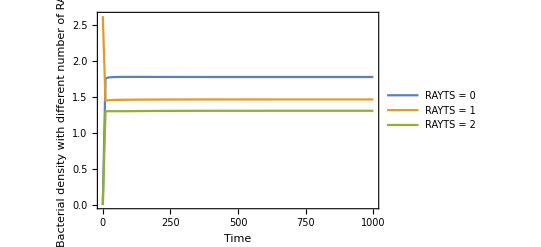

```mathematica
ListPlot[{Table[toplrawrayts02⟦i⟧⟦All,2⟧,{i,1,kmax,1}]//Total,Table[toplrawrayts02⟦i⟧⟦All,2⟧,{i,kmax+1,2 kmax,1}]//Total,Table[toplrawrayts02⟦i⟧⟦All,2⟧,{i,2 kmax+1,3 kmax,1}]//Total},Joined->True,Frame->True,DataRange->{0,1000},FrameLabel->{"Time","Bacterial density with different number of RAYTS"},PlotLegends->{"RAYTS = 0","RAYTS = 1","RAYTS = 2"}]
```